# EPR Function Librariy

## Gauss

```mathematica
G[x]=1/(√(2π)w)ⅇ^(-(x-x0)^2/(2 w^2))
```

Plot

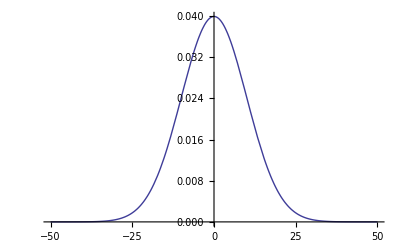

```mathematica
w=10;Plot[1/(√(2π)w)ⅇ^(-x^2/(2 w^2)),{x,-50,50}]
```

```mathematica
w=10;x0=50;a = Table[{10x,1/(√(2π)w)ⅇ^(-(x-x0)^2/(2 w^2))},{x,0,100}]//N;
Export["C:\\Science\\Disp.dat",a]
```

C:\Science\Disp.dat

Normalization

```mathematica
Integrate[1/(√(2π)w)ⅇ^(-x^2/(2 w^2)),{x,-∞,∞}]
```

1

Peak-To-Peak

```mathematica
Solve[D[-(ⅇ^(-x^2/(2 w^2)) x)/(√(2 π) w^3),x]==0,x]
```

{{x→-w},{x→w}}

```mathematica
A=Integrate[1/(√(2π)w)ⅇ^(-x^2/(2 w^2)),{x,-∞,-w},Assumptions->w>0]//N
B=Integrate[1/(√(2π)w)ⅇ^(-x^2/(2 w^2)),{x,-w,w},Assumptions->w>0]//N
```

0.158655

0.682689

```mathematica
B/(2A)//N
```

2.15149

FWHM

```mathematica
Solve[1/(√(2π)w)ⅇ^(-x^2/(2 w^2))==1/(2 √(2π)w),x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→-w √(2 Log[2])},{x→w √(2 Log[2])}}

```mathematica
2Log[2]//N
```

1.38629

Derivative

```mathematica
D[1/(√(2π)w)ⅇ^(-(x-x0)^2/(2 w^2)),x]
```

-(ⅇ^(-(x-x0)^2/(2 w^2)) (x-x0))/(√(2 π) w^3)

```mathematica
dG[x]=-1/(√(2 π) w^3)ⅇ^(-(x-x0)^2/(2 w^2)) (x-x0)
```

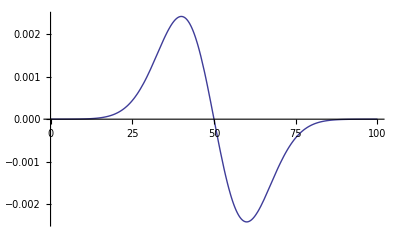

```mathematica
w=10;x0=50;Plot[-1/(√(2 π) w^3)ⅇ^(-(x-x0)^2/(2 w^2)) (x-x0),{x,0,100}]
```

```mathematica
w=10;x0=50;a = Table[{10x,-1/(√(2 π) w^3)ⅇ^(-(x-x0)^2/(2 w^2)) (x-x0)},{x,0,100}]//N;
Export["C:\\Science\\Disp.dat",a]
```

C:\Science\Disp.dat

Dispersion

```mathematica
HilbertTransform: ⅇ^(-x^2)->- ⅇ^(-y^2)Erfi[y]
```

```mathematica
H[x]=-1/(√(2π)w)ⅇ^(-(x-x0)^2/(2 w^2))Erfi[(x-x0)/(√2 w)]
```

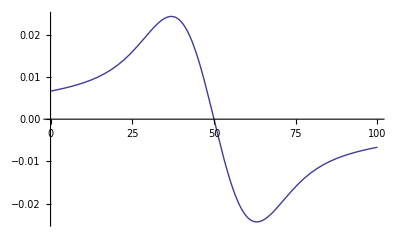

```mathematica
w=10;x0=50;Plot[-1/(√(2π)w)ⅇ^(-(x-x0)^2/(2 w^2))Erfi[(x-x0)/(√2 w)],{x,0,100}]
```

```mathematica
w=10;x0=50;a = Table[{10x,-1/(√(2π)w)ⅇ^(-(x-x0)^2/(2 w^2))Erfi[(x-x0)/(√2 w)]},{x,0,100}]//N;
Export["C:\\Science\\Disp.dat",a]
```

C:\Science\Disp.dat

```mathematica
D[-1/(√(2π)w)ⅇ^(-(x-x0)^2/(2 w^2))Erfi[(x-x0)/(√2 w)],x]
```

-1/(π w^2)+(ⅇ^(-(x-x0)^2/(2 w^2)) (x-x0) Erfi[(x-x0)/(√2 w)])/(√(2 π) w^3)

```mathematica
dH[x]=1/(√(2π)w^3)ⅇ^(-(x-x0)^2/(2 w^2))(x-x0)Erfi[(x-x0)/(√2 w)]-1/(π w^2)
```

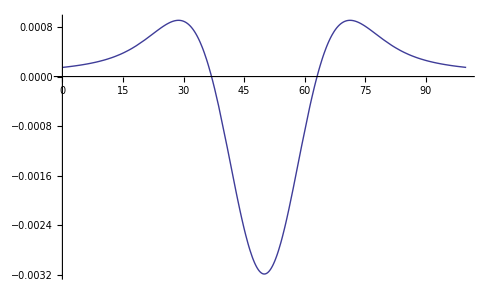

```mathematica
w=10;x0=50;Plot[1/(√(2π)w^3)ⅇ^(-(x-x0)^2/(2 w^2))(x-x0)Erfi[(x-x0)/(√2 w)]-1/(π w^2),{x,0,100}]
```

```mathematica
w=10;x0=250;a = Table[{10x,2/(√(2π)w^3)ⅇ^(-(x-x0)^2/(2 w^2))(x-x0)Erfi[(x-x0)/(√2 w)]-2/(π w^2)},{x,0,500}]//N;
Export["C:\\Science\\Disp.dat",a]
```

C:\Science\Disp.dat

Moments

```mathematica
G[x,x0,w]:=A 1/(√π w)ⅇ^(-(x-x0)^2/w^2)
M0=Integrate[G [x,x0,w],{x,-∞,∞},Assumptions->{w >0,Im[x0] ==0}]
```

A

```mathematica
M1=Integrate[x G [x,x0,w],{x,-∞,∞},Assumptions->{w >0,Im[x0] ==0}]/M0
```

x0

```mathematica
M2=Integrate[(x-x0)^2 G [x,x0,w],{x,-∞,∞},Assumptions->{w >0,Im[x0] ==0}]/M0
```

w^2/2

## Lorentz

```mathematica
L[x]=1/π(1/2 Γ)/((x-x0)^2+(1/2 Γ)^2)=2/π Γ/(4(x-x0)^2+Γ^2)
```

Plot

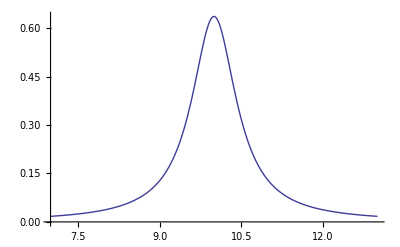

```mathematica
w=1;xc=10;Plot[2/π w/(4(x-xc)^2+w^2),{x,7,13}]
```

FWHM vs Peak-to-Peak

FWHM

```mathematica
Solve[2/π Γ/(4(x-x0)^2+Γ^2)==1/2 2/(π Γ),x]
```

{{x→1/2 (2 x0-Γ)},{x→1/2 (2 x0+Γ)}}

Peak to Peak

```mathematica
Solve[D[-(16 w (x-xc))/(π (w^2+4 (x-xc)^2)^2),x]==0,x]
```

{{x→1/6 (-√3 w+6 xc)},{x→1/6 (√3 w+6 xc)}}

```mathematica
w_pp = 1/(√3)w_fwhm
```

Expression for Peak to Peak linewidth

```mathematica
Subscript[dL, PP][x]=-(16 √3 w (x-xc))/(π (3 w^2+4 (x-xc)^2)^2)
```

```mathematica
Integrate[-(16 √3 w (x-xc))/(π (3 w^2+4 (x-xc)^2)^2),x]
```

```mathematica
(2 √3 w)/(π (3 w^2+4 (x-xc)^2))
```

```mathematica
w=300;xc=3030;Integrate[(2 √3 w)/(π (3 w^2+4 (x-xc)^2)),{x,-∞,∞} ]
```

1

```mathematica
Solve[D[-(16 √3 w (x-xc))/(π (3 w^2+4 (x-xc)^2)^2),x]==0,x]
```

{{x→1/2 (-w+2 xc)},{x→1/2 (w+2 xc)}}

Normalization

```mathematica
w=4; NIntegrate[2/π w/(4(x-xc)^2+w^2),{x,-∞,∞}]
```

1.

Derivative

```mathematica
D[2/π w/(4(x-xc)^2+w^2),x]
```

-(16 w (x-xc))/(π (w^2+4 (x-xc)^2)^2)

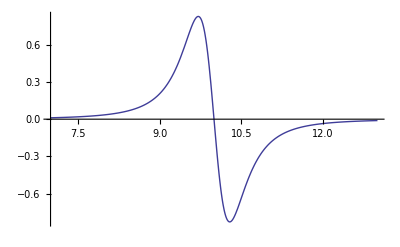

```mathematica
w=1;xc=10;Plot[-(16 w (x-xc))/(π (w^2+4 (x-xc)^2)^2),{x,7,13}]
```

Dispersion

```mathematica
HilbertTransform: 1/(1+x^2)->- y/(1+y^2)
2/(π Γ)1/(1+((2(x-x0))/Γ)^2)-> -2/(π Γ)((2(x-x0))/Γ)/(1+((2(x-x0))/Γ)^2)= -2/π(2(x-x0))/(4(x-x0)^2+Γ^2)
Dis = -2/π(2(x-x0))/(4(x-x0)^2+Γ^2)
```

```mathematica
dDis = -2/π D[(2(x-x0))/(4(x-x0)^2+Γ^2),x]
```

-(2 (-(16 (x-x0)^2)/((4 (x-x0)^2+Γ^2)^2)+2/(4 (x-x0)^2+Γ^2)))/π

```mathematica
dDis =-2/π(-(16 (x-x0)^2)/((4 (x-x0)^2+Γ^2)^2)+2/(4 (x-x0)^2+Γ^2))
```

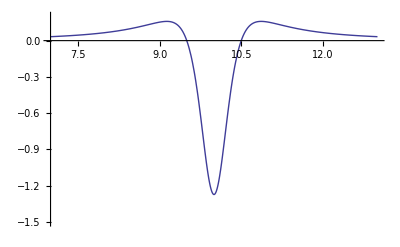

```mathematica
w=1;x0=10;Plot[(32 (x-x0)^2)/(π (4 (x-x0)^2+w^2)^2)-4/(π (4 (x-x0)^2+w^2)),{x,7,13},PlotRange->{-1.5,0.2}]
```

## Dyson

```mathematica
Dy = 2/π((Γ Cos[ϕ]-2(x-x0)Sin [ϕ])/(4(x-x0)^2+Γ^2))
```

(2 (Γ Cos[ϕ]-2 (-10+x) Sin[ϕ]))/(π (4 (-10+x)^2+Γ^2))

Plot

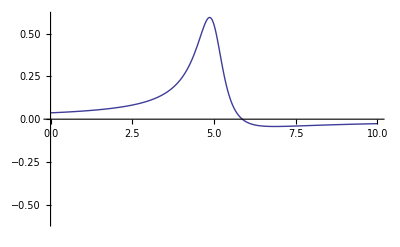

```mathematica
Γ=1;x0 = 5;ϕ = 30/180*π;Plot[2/π((Γ Cos[ϕ]-2(x-x0)Sin [ϕ])/(4(x-x0)^2+Γ^2)),{x,0,10},PlotRange->{-0.6,0.6}]
```

Normalization

```mathematica
Γ=1;x0 = 5;ϕ = 30/180*π;Integrate[2/π((Γ Cos[ϕ]-2(x-x0)Sin [ϕ])/(4(x-x0)^2+Γ^2)),{x,-1000000,1000000}]//N
```

0.866027

Derivative

```mathematica
dDy = D[2/π((Γ Cos[ϕ]-2(x-x0)Sin [ϕ])/(4(x-x0)^2+Γ^2)),x]
```

-(4 Sin[ϕ])/(π (4 (x-x0)^2+Γ^2))-(16 (x-x0) (Γ Cos[ϕ]-2 (x-x0) Sin[ϕ]))/(π (4 (x-x0)^2+Γ^2)^2)

```mathematica
dDy =-4/π((4 (x-x0) (Γ Cos[ϕ]-2 (x-x0) Sin[ϕ]))/((4 (x-x0)^2+Γ^2)^2)+Sin[ϕ]/(4 (x-x0)^2+Γ^2))
```

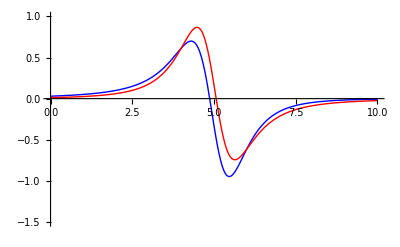

```mathematica
a=4;w=2;x0=5;ϕ = 15/180*π;
A=Plot[-4/π a((4 (x-x0) (w Cos[ϕ]-2 (x-x0) Sin[ϕ]))/((4 (x-x0)^2+w^2)^2)+Sin[ϕ]/(4 (x-x0)^2+w^2)),{x,0,10},PlotRange->{-1.5,1},PlotStyle->Blue];
B=Plot[(2a)/(π w^2)(-4((2(x-x0))/w)Cos[ϕ]+(1-((2(x-x0))/w)^2)Sin [ϕ])/((1+((2(x-x0))/w)^2)^2),{x,0,10},PlotRange->{-1.5,1},PlotStyle->Red];
Show[A,B]
```

## 1D System

```mathematica
Integrate[ ⅇ^(-t^(3/2))Cos[ω t],{t,-∞,∞}]
```

If[ω∈Reals,-1/9 ⅈ (-3 ⅈ+√3) Gamma[-1/3] HypergeometricPFQ[{5/12,11/12},{1/3,1/2,5/6},-(4 ω^6)/729]+7/486 (3-ⅈ √3) ω^4 Gamma[1/3] HypergeometricPFQ[{13/12,19/12},{7/6,3/2,5/3},-(4 ω^6)/729],Integrate[ⅇ^(-t^(3/2)) Cos[t ω],{t,-∞,∞},Assumptions→Im[ω]<0||Im[ω]>0]]

```mathematica
B ∫ⅇ^(-A t^(3/2)) Cos[t ω]ⅆt
```

B ∫ⅇ^(-A t^(3/2)) Cos[t ω]ⅆt

```mathematica
FourierCosTransform[Exp[-A t^(3/2)]Cos[ω t],t,ω]
```

FourierCosTransform[ⅇ^(-A t^(3/2)) Cos[t ω],t,ω]

```mathematica
Integrate[ⅇ^(-A t^(3/2)) Exp[I t ω],{t,-∞,∞}]
```

If[Im[ω]<0,1/3 (ⅈ+(-1)^(1/6)) (3 (-ⅈ+(-1)^(1/6)) Gamma[5/3] Hypergeometric1F1[5/6,2/3,-(4 ⅈ ω^3)/27]+2 ω Gamma[4/3] Hypergeometric1F1[7/6,4/3,-(4 ⅈ ω^3)/27]),Integrate[ⅇ^(-t^(3/2)+ⅈ t ω),{t,-∞,∞},Assumptions→Im[ω]≥0]]

```mathematica
Integrate[ⅇ^(-t^(3/2)+ⅈ t ω),{t,-∞,∞},Assumptions->Im[ω]≥0]
```

If[ω∈Reals,1/162 (2 (-3 ⅈ+√3) Gamma[2/3] (27 ⅈ HypergeometricPFQ[{5/12,11/12},{1/3,1/2,5/6},-(4 ω^6)/729]+5 ω^3 HypergeometricPFQ[{11/12,17/12},{5/6,4/3,3/2},-(4 ω^6)/729])+(3 ⅈ+√3) ω Gamma[4/3] (54 HypergeometricPFQ[{7/12,13/12},{1/2,2/3,7/6},-(4 ω^6)/729]-7 ⅈ ω^3 HypergeometricPFQ[{13/12,19/12},{7/6,3/2,5/3},-(4 ω^6)/729])),Integrate[ⅇ^(-t^(3/2)+ⅈ t ω),{t,-∞,∞},Assumptions→Im[ω]>0]]

```mathematica
If[A>0,1/(162 A^(10/3))(81 (3+ⅈ √3) A^(8/3) Gamma[5/3] HypergeometricPFQ[{5/12,11/12},{1/3,1/2,5/6},-(4 ω^6)/(729 A^4)]+7 (3-ⅈ √3) ω^4 Gamma[4/3] HypergeometricPFQ[{13/12,19/12},{7/6,3/2,5/3},-(4 ω^6)/(729 A^4)]),Integrate[ⅇ^(-A t^(3/2)) Exp[I t ω],{t,-∞,∞},Assumptions->ω∈Reals&&A≤0]]
```

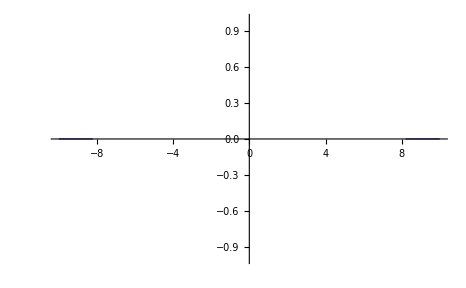

```mathematica
A=1;Plot[-1/9 ⅈ (-3 ⅈ+√3) Gamma[-1/3] HypergeometricPFQ[{5/12,11/12},{1/3,1/2,5/6},-(4 ω^6)/729]+7/486 (3-ⅈ √3) ω^4 Gamma[1/3] HypergeometricPFQ[{13/12,19/12},{7/6,3/2,5/3},-(4 ω^6)/729],{ω,-10,10}]
```